```mathematica
<<xlr8r.m;
<<Cellzilla2D.m;
$HistoryLength=5;
```

xCellerator 0.92 (11-Nov-2012) loaded Mon 12 Nov 2012 16:13:06
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

Cellzilla2D (3.0.0 (11-Nov-2012)) loaded Mon 12 Nov 2012 16:13:06
using xCellerator 0.92 and XSSA 1204002
GPL License Terms Apply

## Define a template with two cells

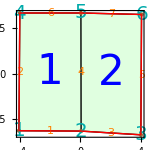

```mathematica
q=RandomizeTemplate[TemplateRectangular[{-4,4, 4},{-2, 2, 4}],.05];
Q=Tissue2DTissue[q];
ShowTissue[Q, "CellNumbers"-> True, "EdgeNumbers"-> True,
"CellNumberStyle"-> {Blue,42}, "BoundaryStyle"-> Red,
"EdgeNumberStyle"-> Orange,"Vertices"-> {Brown,PointSize[.02]},
"Nucleus"-> False, "VertexNumbers"-> True,"VertexNumberStyle"-> {20,Darker[Cyan]},
Frame-> True,BaseStyle-> {FontSize-> 17}, ImageSize-> 150]
```

## Define the network and the network parameters

```mathematica
network={{A⇄∅,kA, dA}, {P⇄∅, kP,dP}};
diff={{A, βout, βin, βw}};
pumps={{P, Fout, Fin}};
parameters={dA->0.1,kA->.1,kP-> .1, dP-> .1, halfwall->.025,DA->700,k->10,μ->1,pressure->1.5, Fout-> 1, Fin-> 1, βin-> 1, βout-> 1, βw-> 1};
wall={{A-> ∅, kA}};
```

## Run the simulation

simdir = /home/mathman/Simulations-12-Nov-12/test-12Nov12-1548

Tissue snapshot written to /home/mathman/Simulations-12-Nov-12/test-12Nov12-1548/Snapshot0001.png

Actual Clock Time:  | 12-Nov-2012-at-15:48:56
Memory in Use (GB):  | 0.0462112
Max Memory Used (GB):  | 0.0479292
Free Memory (GB):  | 18.9977

Cell 1 (static cell 1) divides at t = 2.09787

Tissue snapshot written to /home/mathman/Simulations-12-Nov-12/test-12Nov12-1548/Snapshot0002.png

Actual Clock Time:  | 12-Nov-2012-at-15:48:57
Memory in Use (GB):  | 0.0519174
Max Memory Used (GB):  | 0.0538518
Free Memory (GB):  | 18.9833
CPU Used(seconds):  | 1.11207
Number of Cells:  | 3
Cell Divisions:  | 1
Simulator Steps:  | 2
Number of Variables:  | 51

Cell 2 (static cell 2) divides at t = 2.1124

Tissue snapshot written to /home/mathman/Simulations-12-Nov-12/test-12Nov12-1548/Snapshot0003.png

Actual Clock Time:  | 12-Nov-2012-at-15:48:58
Memory in Use (GB):  | 0.0525706
Max Memory Used (GB):  | 0.0549339
Free Memory (GB):  | 18.9852
CPU Used(seconds):  | 2.80018
Number of Cells:  | 4
Cell Divisions:  | 2
Simulator Steps:  | 3
Number of Variables:  | 75

Cell 4 (static cell 4) divides at t = 3.51665

Tissue snapshot written to /home/mathman/Simulations-12-Nov-12/test-12Nov12-1548/Snapshot0004.png

Actual Clock Time:  | 12-Nov-2012-at-15:48:59
Memory in Use (GB):  | 0.0540785
Max Memory Used (GB):  | 0.0564922
Free Memory (GB):  | 18.98
CPU Used(seconds):  | 4.60029
Number of Cells:  | 5
Cell Divisions:  | 3
Simulator Steps:  | 4
Number of Variables:  | 99

Cell 1 (static cell 1) divides at t = 3.94552

Tissue snapshot written to /home/mathman/Simulations-12-Nov-12/test-12Nov12-1548/Snapshot0005.png

Actual Clock Time:  | 12-Nov-2012-at-15:49:01
Memory in Use (GB):  | 0.0553216
Max Memory Used (GB):  | 0.0588889
Free Memory (GB):  | 18.9753
CPU Used(seconds):  | 6.10838
Number of Cells:  | 6
Cell Divisions:  | 4
Simulator Steps:  | 5
Number of Variables:  | 123

Cell 3 (static cell 3) divides at t = 4.05208

Tissue snapshot written to /home/mathman/Simulations-12-Nov-12/test-12Nov12-1548/Snapshot0006.png

Actual Clock Time:  | 12-Nov-2012-at-15:49:03
Memory in Use (GB):  | 0.0569047
Max Memory Used (GB):  | 0.0608563
Free Memory (GB):  | 18.9729
CPU Used(seconds):  | 7.80849
Number of Cells:  | 7
Cell Divisions:  | 5
Simulator Steps:  | 6
Number of Variables:  | 147

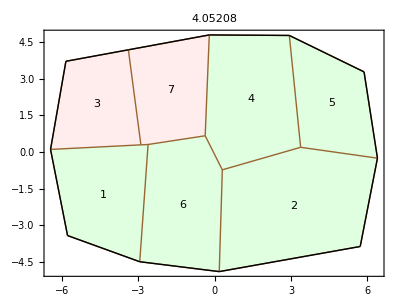

Simulation Completed at t = 4.05208 after 5 cell divisions; Normal Exit.

```mathematica
SIM=grow[Q,0,10,

"Walls"-> True, 
"TestCase"-> "test", 
"SaveODES"-> True,
"SaveEquations"-> True, 
"MaxDivisions"-> 5, 
"Reactions"-> network, 
"Pumps"-> pumps,
"Diffusion"-> diff, 
"WallReactions"->wall,
 "BoundaryConditions"-> {A-> .1}, 
"Growing"-> True,
"Weights"-> {1,1,0,0},  
"Parameters"-> parameters, 
"DivisionThreshold"-> 25, 
"Verbose"-> False];
```

## Examine the simulation folder

```mathematica
$SIMDIR
```

/home/mathman/Simulations-12-Nov-12/test-12Nov12-1548

```mathematica
Short[ShowSavedFiles[], 5]
```

{/home/mathman/Simulations-12-Nov-12/test-12Nov12-1548/DTissue0001.nb,«33»,/home/mathman/Simulations-12-Nov-12/test-12Nov12-1548/TimeSpans.nb}

```mathematica
ShowSavedFiles["ODE"]
```

{/home/mathman/Simulations-12-Nov-12/test-12Nov12-1548/ODES0001.nb,/home/mathman/Simulations-12-Nov-12/test-12Nov12-1548/ODES0002.nb,/home/mathman/Simulations-12-Nov-12/test-12Nov12-1548/ODES0003.nb,/home/mathman/Simulations-12-Nov-12/test-12Nov12-1548/ODES0004.nb,/home/mathman/Simulations-12-Nov-12/test-12Nov12-1548/ODES0005.nb}

```mathematica
Short[GetSavedFile[$SIMDIR, "Net",1], 5]
```

/home/mathman/Simulations-12-Nov-12/test-12Nov12-1548/Network0001.nb

{{A[1]→∅,kA},{∅→A[1],dA},{P[1]→∅,kP},{∅→P[1],dP},«106»,{∅→y[5],0.5 pressure (-x[4][t]+x[6][t])},{∅→x[6],-0.5 pressure (y[3][t]-y[5][t])},{∅→y[6],-0.5 pressure (-x[3][t]+x[5][t])}}